```mathematica
paises = indicador[[2,;;,4]];
paises =Append[paises, Regiones[[2]]];


migrationa = Table[{i+1953,indicador[[2,;;,i]]},{i,9,97,5}];

migrationa[[2]]
```

{1967,{-99,103399,-40000,65585,-96958,-6423,-1225,85196,173343,,104185,-28981,74449,-53773,-2001,-553217,,25884,-179999,28147,267629,444282}}

```mathematica
migrationa2 = Table[Append[migrationa[[i,2]],Total@(Replace[#,Except[_?NumberQ]->0,{1}]&@ migrationa[[i,2]])],{i,1,migrationa//Length}] ;
migrationa2[[2]]
```

{-99,103399,-40000,65585,-96958,-6423,-1225,85196,173343,,104185,-28981,74449,-53773,-2001,-553217,,25884,-179999,28147,267629,444282,409423}

```mathematica
plots = Table[BarChart[migrationa2[[i]], ChartLabels->paises, ChartStyle->"DarkRainbow",PlotRange->{-500000,1500000},PlotLabel->"Net Migration"migrationa[[i,1]]],{i,1,migrationa//Length}];
```

```mathematica
indicador[[1,11]]
```

```mathematica
Total@(Replace[#,Except[_?NumberQ]->0,{1}]&@ migrationa[[2,2]])
```

409423

```mathematica
ListAnimate[plots]
```

```mathematica
Export["migration1.svg",plots[[5]]]
```

migration1.svg

```mathematica
paises
```

{ALB,ARM,AZE,BLR,BIH,BGR,HRV,GEO,KAZ,XKX,KGZ,MKD,MDA,MNE,ROU,RUS,SRB,TJK,TUR,TKM,UKR,UZB}

```mathematica
Export["migration2.pdf",Graphics[plots[[5]],Background->None]]
```

migration2.pdf

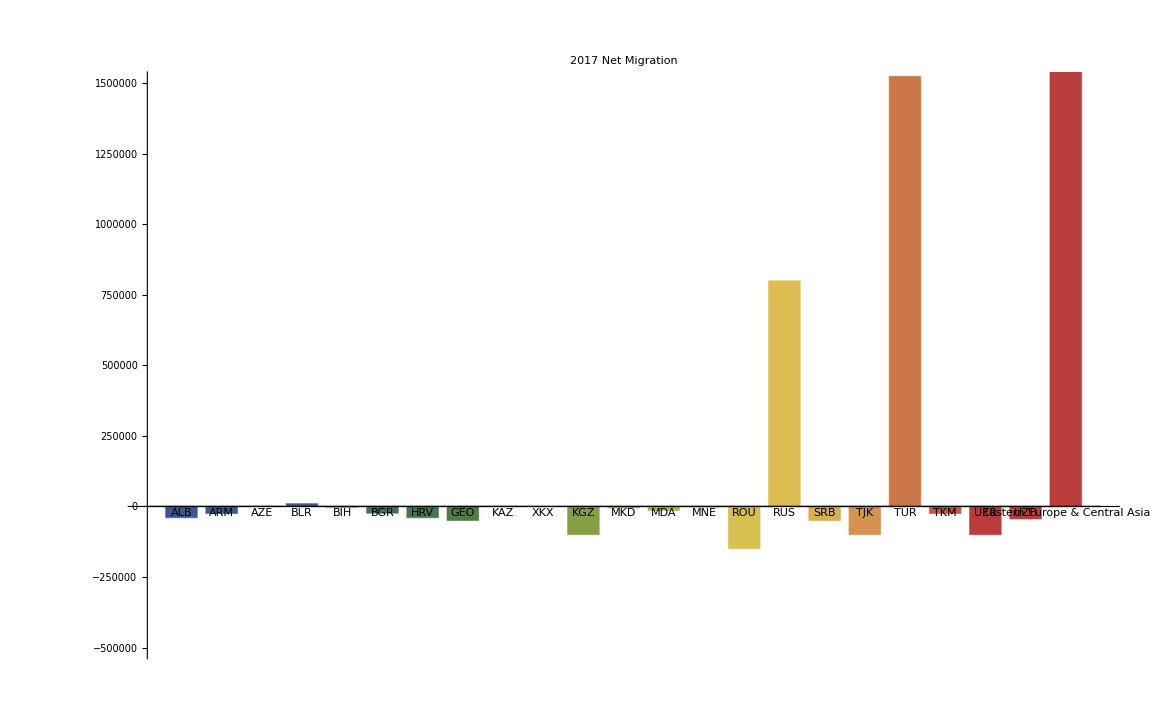

```mathematica
plots[[-7]]
```